```mathematica
Quit
```

```mathematica
PacletDirectoryLoad[FileNameJoin[{ParentDirectory@NotebookDirectory[],"packages"}]]
```

{/Users/christopher/git/ComputationalDiaries/packages}

```mathematica
Needs["AstronomicalDiaries`"]
```

```mathematica
dataDirectory=FileNameJoin[{ParentDirectory[NotebookDirectory[]],"data"}]
```

/Users/christopher/git/ComputationalDiaries/data

## Loading the raw data

https://web.archive.org/web/20070808121203/http://www.chass.utoronto.ca/~ajones/normal_stars/

https://web.archive.org/web/20070812093739/http://www.chass.utoronto.ca/~ajones/normal_stars/Collection_A.txt

https://web.archive.org/web/20070811220734/http://www.chass.utoronto.ca/~ajones/normal_stars/Collection_B.txt

https://web.archive.org/web/20070811221745/http://www.chass.utoronto.ca/~ajones/normal_stars/normal_star_data.txt

```mathematica
rawTXT=Import[FileNameJoin[{dataDirectory,"jones","Collection_A.txt"}]];
```

```mathematica
rawCSV=AssociationThread[StringSplit[StringSplit[rawTXT,"\n"][[26]],","],#]&/@ImportString[StringRiffle[StringSplit[rawTXT,"\n"][[27;;]],"\n"],"CSV"][[All,;;23]];
```

## Converting events

```mathematica
StringTake[rawTXT,1168]
```

Text,Identifies text: Diaries by year number; texts in vol 5 by text number; GYTs by tablet inventory number
Obj,planet
T_Era,king for regnal year or SE for Seleucid Era
T_Y,year number in Babylonian calendar
T_M,month number in Bab calendar
T_D,day number in Bab calendar
T_T,f = first part of night; l = last part of night
NS_Id,identifies normal star
NS_No,number of normal star in Sachs-Hunger list
Up,Y if there is a measurement above or below
Up_C,number of cubits; positive means above; negative means below
Up_F,number of fingers
Ahead,Y if there is a measurement behind or in front
Ahead_C,number of cubits; positive means behind; negative means in front
Ahead_F,number of fingers
Notes,miscellaneous including indication of uncertain readings or corrections to text
J_Y,Julian year number using astronomical convention -x = x+1 B.C.
J_M,number of Julian month
J_D,number of Julian calendar day; always the number of the day preceding the night
P_Long,tropical longitude from JPL ephemeris; midnight for outer planets; 4 hours before or after midnight for inners; midnight = 21 UT
P_Lat,latitude from JPL
NS_Long,tropical longitude of NS
NS_Lat,latitude of NS

```mathematica
normalStarNames=GetNormalStars/@<|"hPsc"->"EtaPiscium","bAri"->"BetaArietis","aAri"->"AlphaArietis","hTau"->"EtaTauri","aTau"->"AlphaTauri","bTau"->"BetaTauri","zTau"->"ZetaTauri","hGem"->"EtaGeminorum","mGem"->"MuGeminorum","gGem"->"GammaGeminorum","aGem"->"AlphaGeminorum","bGem"->"BetaGeminorum","hCnc"->"EtaCancri","thCnc"->"ThetaCancri","gCnc"->"GammaCancri","dCnc"->"DeltaCancri","eLeo"->"EpsilonLeonis","aLeo"->"AlphaLeonis","rLeo"->"RhoLeonis","thLeo"->"ThetaLeonis","bVir"->"BetaVirginis","gVir"->"GammaVirginis","aVir"->"AlphaVirginis","aLib"->"AlphaLibrae","bLib"->"BetaLibrae","dSco"->"DeltaScorpii","bSco"->"BetaScorpii","aSco"->"AlphaScorpii","thOph"->"ThetaOphiuchi","bCap"->"BetaCapricorni","gCap"->"GammaCapricorni","dCap"->"DeltaCapricorni"|>;
```

```mathematica
planetNames=<|"Mercury"->Entity["Planet","Mercury"],"Venus"->Entity["Planet","Venus"],"Mars"->Entity["Planet","Mars"],"Jupiter"->Entity["Planet","Jupiter"],"Saturn"->Entity["Planet","Saturn"]|>;
```

```mathematica
rationalize[n_]:=IntegerPart[n]+Nearest[{0->0,0.5->1/2,0.67->2/3,0.83->5/6},FractionalPart[n]][[1]]
rationalize[_Missing]:=Missing[]
```

```mathematica
jonesEvents = Function[e,
	DiaryEvent[<|
		"Type"->"RelativePosition",
		"Provenance"-><|
			"Tablet"->e["Text"],
			"Line"->Missing[],
			"Creator"->"Alexander Jones Processor",
			"Reviewed"->False,
			"Notes"->"Automatically generated from Alexander Jones's data"
		|>,
		"Content"-><|
			"Source"->Lookup[planetNames,e["Obj"],Missing[]],
			"Target"->Lookup[normalStarNames,e["NS_Id"],Missing[]],
			"Date"->DiaryDate[<|
				"JulianYear"->e["J_Y"],
				"JulianMonth"->e["J_M"],
				"JulianDay"->e["J_D"],
				"BabylonianYear"->{e["T_Y"],e["T_Era"]},
				"BabylonianMonth"->If[NumberQ[e["T_M"]],Floor[e["T_M"]],Missing[]](*NEED TO CHANGE SPEC*),
				"BabylonianDay"->e["T_D"],
				"Time"->Switch[e["T_T"],"f","FirstPartOfTheNight","l","LastPartOfTheNight",_,Missing[]]
			|>],
			"Displacement"->DiaryDisplacement[{
				{
					DiaryDistance[{rationalize[e["Up_C"]/.""->Missing[]],e["Up_F"]/.""->Missing[]}/.n_?NumberQ:>Abs[n]],
					If[Sign[e["Up_C"]]===-1 || Sign["Up_F"]===-1,"Below","Above"]
				},
				{
					DiaryDistance[{rationalize[e["Ahead_C"]/.""->Missing[]],e["Ahead_F"]/.""->Missing[]}/.n_?NumberQ:>Abs[n]],
					If[Sign[e["Ahead_C"]]===-1 || Sign["Ahead_F"]===-1,"InFrontOf","Behind"]
				}
			}]
		|>
	|>]
]/@rawCSV;
```

```mathematica
Union@rawCSV[[All,"T_M"]]
```

{1,2,3,4,5,6,6.2,7,8,9,10,11,12,12.2,}

```mathematica
jonesEvents[[10]]
```

DiaryEvent[<|Type→RelativePosition,Provenance→<|Tablet→-321,Line→Missing[],Creator→Alexander Jones Processor,Reviewed→False,Notes→Automatically generated from Alexander Jones's data|>,Content→<|Source→Jupiter,Target→ρ Leonis,Date→DiaryDate[…],Displacement→DiaryDisplacement[…]|>|>]

```mathematica
ReverseSort@Counts[#["Content"]["Target"]&/@jonesEvents]
```

<|Regulus→73,Tejat→70,Alnath→68,Pollux→67,Spica→66,Alhena→62,Propus→60,Porrima→59,Castor→57,ρ Leonis→57,Alaraph→56,ξ Tauri→56,θ Ophiuchi→54,ϵ Leonis→53,α 1 Librae→53,Dabih→49,Antares→48,Chort→46,Alcyone→46,Nashira→46,Aldebaran→45,Hamal→44,Asellus Australis→44,Deneb Algiedi→42,Zubeneshamali→41,β 2 Scorpii→40,η Piscium→39,Sheratan→39,Dschubba→18,Asellus Borealis→10,η Cancri→9,θ Cancri→9,Missing[]→1|>

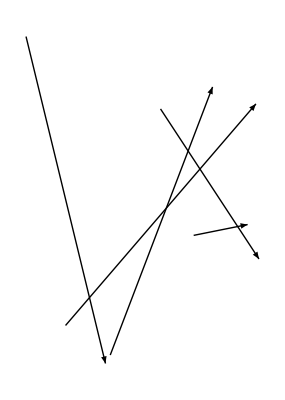

```mathematica
Graphics[Arrow[{#2,#1+#3}&@@@DeleteMissing[{#["Content"]["Displacement"]["EclipticDisplacement"],AstronomicalPosition[#["Content"]["Source"],#["Content"]["Date"]],AstronomicalPosition[#["Content"]["Target"],#["Content"]["Date"]]}&/@Select[jonesEvents,#["Content"]["Target"]===Entity["Star","Tejat"]&],1,3]]]
```

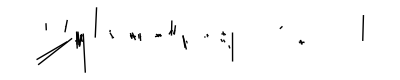

```mathematica
Graphics[Line[{#2,#1+#3}&@@@DeleteMissing[{#["Content"]["Displacement"]["EclipticDisplacement"],AstronomicalPosition[#["Content"]["Source"],#["Content"]["Date"]],AstronomicalPosition[#["Content"]["Target"],#["Content"]["Date"]]}&/@Select[jonesEvents,!MissingQ[#["Content"]["Target"]]&],1,3]]]
```

```mathematica
Length@DeleteMissing[{#["Content"]["Displacement"]["EclipticDisplacement"],AstronomicalPosition[#["Content"]["Source"],#["Content"]["Date"]],AstronomicalPosition[#["Content"]["Target"],#["Content"]["Date"]]}&/@Select[jonesEvents,!MissingQ[#["Content"]["Target"]]&],1,3]
```

71

```mathematica
Select[Values/@rawCSV[[All,{"Up_C","Ahead_C"}]],FreeQ[""]]
```

{{1,0.67},{-2,0.5},{0,-0.5},{-1.67,1},{-3,-0.5},{0,-0.67}}

```mathematica
sourcesTargets={Maybe[AstronomicalPosition][#["Content"]["Source"],#["Content"]["Date"]],Maybe[AstronomicalPosition][#["Content"]["Target"],#["Content"]["Date"]]}&/@jonesEvents;
```

```mathematica
GetNormalStars[]
```

{η Piscium,Sheratan,Hamal,Alcyone,Aldebaran,Alnath,ξ Tauri,Propus,Tejat,Alhena,Castor,Pollux,η Cancri,θ Cancri,Asellus Borealis,Asellus Australis,ϵ Leonis,Regulus,ρ Leonis,Chort,Alaraph,Porrima,Spica,α 1 Librae,Zubeneshamali,Dschubba,β 2 Scorpii,Antares,θ Ophiuchi,Dabih,Nashira,Deneb Algiedi,π Scorpii}

```mathematica
jonesEvents[[1]]["Content"]
```

<|Source→Jupiter,Target→Regulus,Date→DiaryDate[…],Displacement→DiaryDisplacement[…]|>

```mathematica
Position[jonesEvents,e_/;e["Content"]["Target"]===Entity["Star","EtaPiscium"],{1}]
```

{{50},{51},{160},{207},{240},{248},{254},{309},{375},{397},{411},{423},{434},{436},{441},{449},{481},{494},{630},{676},{808},{834},{954},{974},{986},{992},{1013},{1041},{1101},{1121},{1185},{1224},{1242},{1265},{1279},{1297},{1302},{1367},{1425}}

```mathematica
Entity["Constellation","Taurus"][EntityProperty["Constellation","BrightStars"]]
```

{Aldebaran,Alnath,Alcyone,ζ Tauri,θ 2 Tauri,λ Tauri,Ain,ο Tauri,γ Tauri,ξ Tauri,δ 1 Tauri,θ 1 Tauri,ν Tauri,κ 1 Tauri,μ Tauri,τ Tauri,υ Tauri,δ 3 Tauri,ι Tauri,ρ Tauri,σ 2 Tauri,π Tauri,δ 2 Tauri,ω 2 Tauri,ϕ Tauri,σ 1 Tauri,ψ Tauri,κ 2 Tauri,χ Tauri,ω 1 Tauri}

```mathematica
AstronomicalPosition[Entity["Star","ZetaTauri"],DateObject[{-600}]]
```

AstronomicalPosition::invalidObject: ζ Tauri is not a valid normal star or synodic object.

$Failed

```mathematica
GetNormalStars[][[7]]
```

ξ Tauri

```mathematica
Graphics[{Opacity[0.1],Line[Map[{Mod[#[[1]]+25,360],#[[2]]}&,DeleteMissing[Extract[sourcesTargets,Position[jonesEvents,e_/;e["Content"]["Target"]===GetNormalStars[][[7]],{1}]],1,2],{2}]]},PlotRange->{{0,360},{-90,90}}]
```

-Graphics-

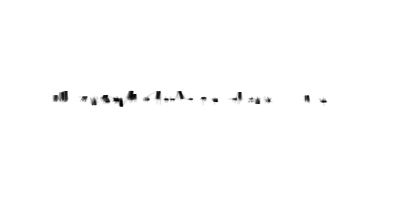

```mathematica
Graphics[{Opacity[0.1],Line[Map[{Mod[#[[1]]+25,360],#[[2]]}&,DeleteMissing[sourcesTargets,1,2],{2}]]},PlotRange->{{0,360},{-90,90}}]
```

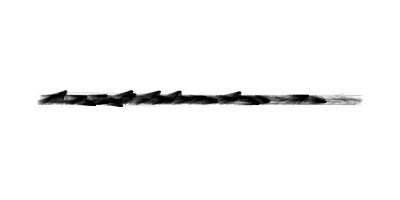

```mathematica
Graphics[{Opacity[0.1],Line[Map[{Mod[#[[1]]+25,360],#[[2]]}&,DeleteMissing[sourcesTargets2,1,2],{2}]]},PlotRange->{{0,360},{-90,90}}]
```

Precession!

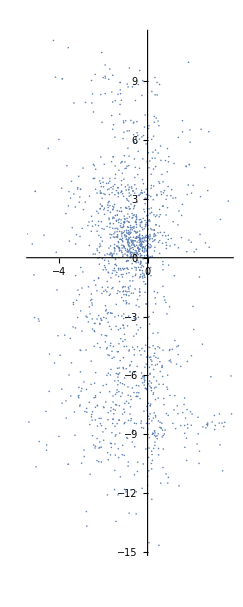

```mathematica
ListPlot[Subtract@@@sourcesTargets,AspectRatio->Automatic]
```

```mathematica
dispSourcesTargets={#["Content"]["Displacement"]["EclipticDisplacement"],Maybe[AstronomicalPosition][#["Content"]["Source"],#["Content"]["Date"]],Maybe[AstronomicalPosition][#["Content"]["Target"],#["Content"]["Date"]]}&/@jonesEvents;
```

```mathematica
dispSourcesTargets2={#["Content"]["Displacement"]["EclipticDisplacement"],Maybe[AstronomicalPosition][#["Content"]["Source"],#["Content"]["Date"]],Maybe[AstronomicalPosition][#["Content"]["Target"],#["Content"]["Date"]]}&/@displacementEvents;
```

```mathematica
sourcesTargets=dispSourcesTargets[[All,2;;]];
```

```mathematica
sourcesTargets2=dispSourcesTargets2[[All,2;;]];
```

```mathematica
DeleteMissing@dispSourcesTargets[[All,2;;]]
```

{{{115.626,0.833609},{116.897,0.358819}},{{216.95,0.816957},{216.739,-4.25936}},{{48.3431,-0.433854},{49.6289,5.1894}},1522,{{157.088,0.616719},{157.925,2.96489}},{{169.869,-0.0464868},{171.283,-1.90214}}}
 |  |  |  |

```mathematica
dispSourcesTargets[[All,1]]
```

{{1/3,-1},{Missing[],-Missing[]},{Missing[],4},{Missing[],-2/3},{Missing[],-2/3},{Missing[],-Missing[]},{4/3,-8/3},{Missing[],-5/12},{Missing[],-1/3},{Missing[],-5/6},{Missing[],-Missing[]},{Missing[],-4},{Missing[],-1/3},{Missing[],4},{Missing[],-Missing[]},1497,{1/4,-1/3},{Missing[],-1/6},{Missing[],-Missing[]},{Missing[],-1},{Missing[],-1},{Missing[],-7/6},{1/3,4},{Missing[],-Missing[]},{1/3,-1/3},{Missing[],-4/3},{Missing[],4},{1/3,-Missing[]},{1/3,-Missing[]},{Missing[],2},{Missing[],-2}}
 |  |  |  |

```mathematica
DeleteMissing[{(#1/.Missing[]->0)+#2,#3}&@@@(dispSourcesTargets),1,4]
```

{{{115.959,-0.166391},{116.897,0.358819}},{{216.95,0.816957},{216.739,-4.25936}},{{48.3431,3.56615},{49.6289,5.1894}},1521,{{157.088,2.61672},{157.925,2.96489}},{{169.869,-2.04649},{171.283,-1.90214}}}
 |  |  |  |

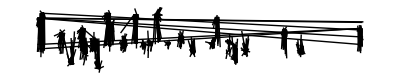

```mathematica
Graphics[Line[DeleteMissing[{(#1/.Missing[]->0)+#2,#3}&@@@(dispSourcesTargets),1,4]]]
```

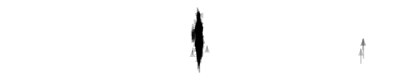

```mathematica
Graphics[{Opacity[0.2],Arrowheads[Small],Arrow[{#2-#3,#2-#3+(#1/.Missing[]->0)}&@@@Delete[dispSourcesTargets,312]]},PlotRange->25]
```

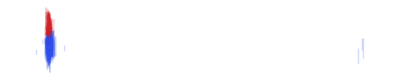

```mathematica
Graphics[{{Orange,Disk[{0,0},0.5]},{Opacity[0.2],{ColorData["TemperatureMap"][Rescale[ArcTan@@(#[[1]]-#[[2]]),{-Pi/2,Pi/2}]],Line[#]}&/@DeleteCases[({#2-#3,#2-#3+(#1/.Missing[]->0)}&@@@Delete[dispSourcesTargets,312]),{x_,x_}]}},PlotRange->25]
```

Incorporate time of night!